# Combine Plots

```mathematica
ClearAll["Global`*"]
```

## Prerequisites

Need to run following codes to generate the data files:

High-T expansion result: phase_transition/highT.nb to generate phase_transition/output/highT.m
Instability scale solution: model_setup/instability.nb to generate model_setup/output/instable_scale.csv

```mathematica
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];
```

## High-T phase transition

```mathematica
DumpGet[NotebookDirectory[]<>"/phase_transition/output/highT.m"]
```

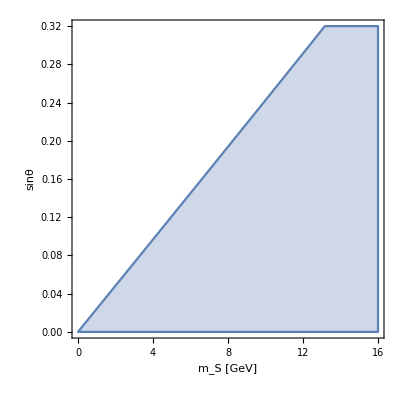

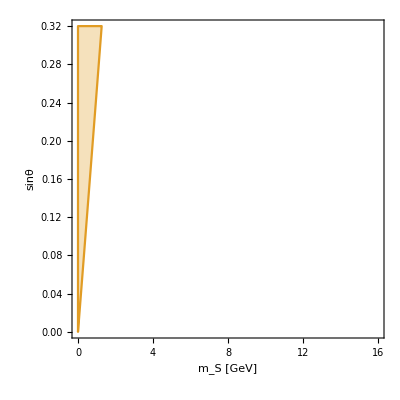

```mathematica
HighT‵SFOPT‵plot=RegionPlot[{strength[mS,sinθ]≤1.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,1],Opacity[0.3]},BoundaryStyle->{ColorData[97,1]}]//cleanRegionPlot
non‵restore‵plot=RegionPlot[{Positive‵factor[mS,sinθ]≤0.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,2],Opacity[0.3]},BoundaryStyle->{ColorData[97,2]}]//cleanRegionPlot
```

## LEP bound

```mathematica
boundlist=Import[NotebookDirectory[]<>"/collider/output/LEPbound.csv"];
boundfunc[mS_]:=Interpolation[boundlist][mS]
```

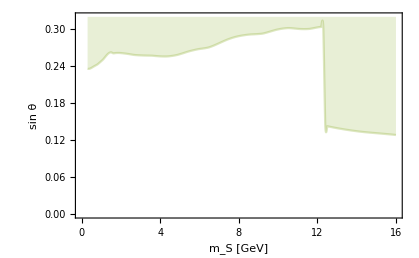

```mathematica
LEP‵plot=Plot[boundfunc[mS],{mS,0.3,16},PlotRange->{{0,16},{0,0.32}},Filling->Top,PlotStyle->{ColorData[97,3],Opacity[0.3]},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

## LHC result

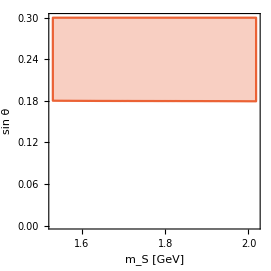

```mathematica
σggF=48.6;(*pb*)
σppH=55.1;(*pb*)
ΓSM=4.07*10^-3;(*GeV*)
mb=4.19;
mc=1.27;
mτ=1.78;
mμ=0.105;
ms=0.093;
mh=125.;
v=174.;
μBR[mS_]:=(mμ^2 Re[(mS^2-4 mμ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]+mμ^2 Re[(mS^2-4 mμ^2)^(3/2)]+3 ms^2 Re[(mS^2-4 ms^2)^(3/2)]);
τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
ghSS[mS_,sinθ_]:=2 √2 λ[mS,sinθ]v sinθ^2-√A2[mS,sinθ] sinθ;
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mh)√(1-4 mS^2/mh^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
dataset=Import[NotebookDirectory[]<>"collider/LHC.csv"];
limit[mS_]:=Interpolation[dataset][mS];
LHCplot=RegionPlot[σggF*BRhSS[mS,sinθ]*μBR[mS]^2>=10^-3 limit[mS],{mS,dataset[[1,1]],dataset[[-1,1]]},{sinθ,0.001,0.3},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,4],Opacity[0.3]},BoundaryStyle->{ColorData[97,4]}]//cleanRegionPlot
```

## Vacuum tunneling trajectory

```mathematica
DumpGet[NotebookDirectory[]<>"model_setup/output/V0T_BPeg.m"]
```

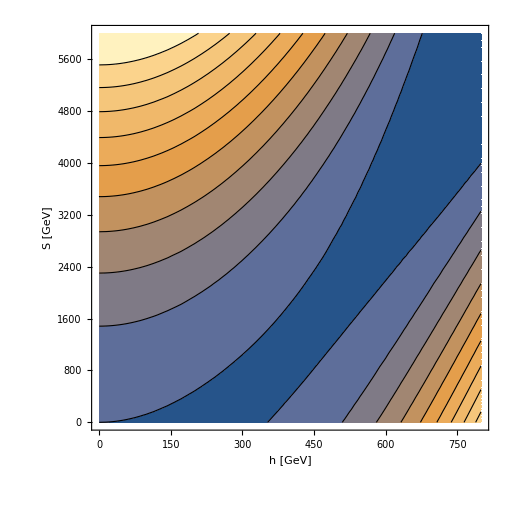

```mathematica
potential=ContourPlot[V0T‵BPeg[h,S],{h,0,800},{S,0,6000},Contours->10,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h [GeV]",FontFamily->"Times",FontSize->18],Style["S [GeV]",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

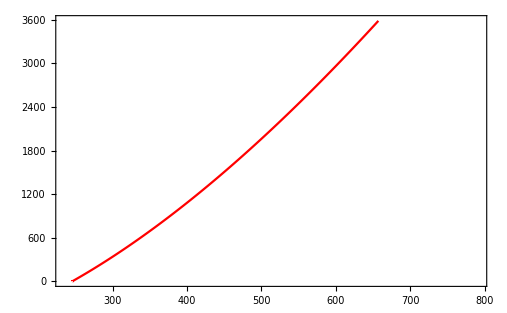

```mathematica
pathdata={100*#2,100*#3}& @@@Import[NotebookDirectory[]<>"model_setup/output/BPeg.csv","Data"][[2;;]];
path=ListLinePlot[pathdata,PlotStyle->Red]
```

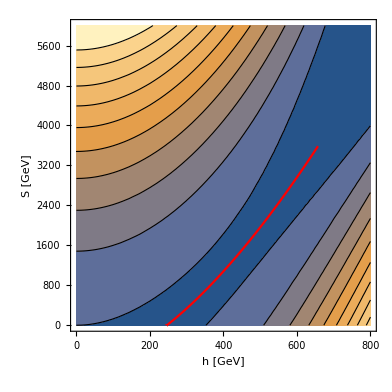

```mathematica
Show[potential,path]
```

```mathematica
potential3d=Plot3D[BP1‵V0T[h,S],{h,0,800},{S,0,6000}]
```

-Graphics3D-

```mathematica
potential‵data=BP1‵V0T @@@ pathdata;
trajectorydata=MapThread[Append,{pathdata,potential‵data}];
```

```mathematica
trajectory=ListLinePlot3D[trajectorydata,PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[potential3d,trajectory]
```

-Graphics3D-

## Fine-tunning contour

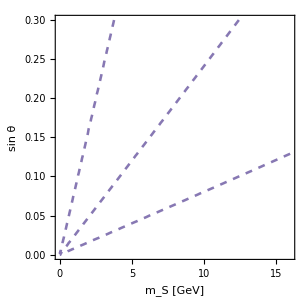

```mathematica
finetuning=ContourPlot[mS^2/(mS^2(1-sinθ^2)+mh^2(sinθ^2)),{mS,0,16},{sinθ,0,0.3},ContourShading->None,Contours->{0.1,0.01,0.5},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},ContourStyle->{Directive[Dashed,ColorData[97,5],Thickness[0.006]]}]
```

## Combine-1

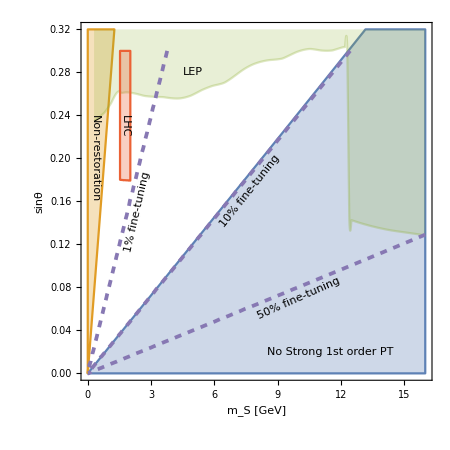

```mathematica
Combine1=Show[HighT‵SFOPT‵plot,non‵restore‵plot,LEP‵plot,LHCplot,finetuning,Epilog->{Inset[Framed[Style["No Strong 1st order PT",ColorData[97,"ColorList"][[1]]],FrameStyle->None],{11.5,0.02}],Inset[Framed[Style["LEP",ColorData[97,"ColorList"][[3]]],FrameStyle->None],{5,0.28}],Inset[Rotate[Framed[Style["LHC",ColorData[97,"ColorList"][[4]]],FrameStyle->None],-90 Degree],{1.75,0.23}],Inset[Rotate[Framed[Style["50% fine-tuning",ColorData[97,"ColorList"][[5]]],FrameStyle->None],24Degree],{10,0.07}],Inset[Rotate[Framed[Style["10% fine-tuning",ColorData[97,"ColorList"][[5]]],FrameStyle->None],51.5Degree],{7.7,0.17}],Inset[Rotate[Framed[Style["1% fine-tuning",ColorData[97,"ColorList"][[5]]],FrameStyle->None],77Degree],{2.37,0.15}],Inset[Rotate[Framed[Style["Non-restoration",ColorData[97,"ColorList"][[2]]],FrameStyle->None],-90 Degree],{0.36,0.2}]},ImageSize->450,Background->White,Axes->None]
Export["/Users/isaac/Dropbox/Research_Project/2022-1-SFOPT_light_singlet/01-Draft/Figures/Combine.pdf",Combine1];
```